# Finite Potential Wells in QM

## Functions

#### Making Wells

This function generates a list of points that corresponds to n wells of between -1 and 1. The wells all have the same width, as do the barriers. They have depth -V0. The function extends from negrinf to -negrinf. Note that some step sizes will not give equally sized wells, thus, it is important to choose a stepsize of appropriate dimension. (Pick a number such that N_0/(4*n) == integer, then subtract 2 from N_0 to get N. An example: If we want 50 wells: try N_0 = 1000. Then 1000/(4*50)=5==integer, so our step size should be N = N_0- 2 = 998.)

```mathematica
VNWellsMod[V0_,n_,Ns_,negrinf_]:=Module[{i,boundaries,wellwidth,V,q0,dq,qdif},
dq=2./(-Ns/negrinf+1);
qdif=Abs[negrinf]-Abs[q0];
q0=-1.;
wellwidth=(2./(2n-1));
V=Table[{negrinf+j dq,0.0},{j,1,Ns}];
For[i=1,i< Ns,i++,
If[(-negrinf/2+0.5)(Ns)/(-negrinf)≥ i≥(-negrinf/2-0.5)(Ns)/(-negrinf), 
If[Mod[i dq+qdif-wellwidth,2wellwidth]< wellwidth,
V[[i+1,2]]=-V0,
V[[i+1,2]]=0];
];
];
Return[V];
]
```

A quick example:

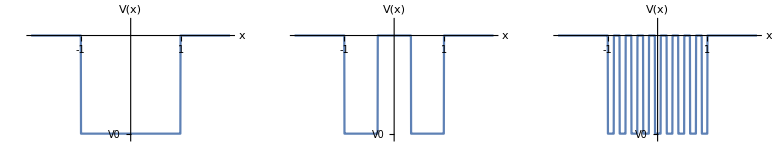

```mathematica
potentials=GraphicsGrid[{{ListLinePlot[VNWellsMod[10,1,998,-2], PlotRange->{{-2,2},{-10.5,01.5}}, Ticks-> {{1,-1},{{-10,"V0"}}},AxesStyle->Larger, AxesLabel->{"x","V(x)"}],
ListLinePlot[VNWellsMod[10,2,998,-2], PlotRange->{{-2,2},{-10.5,01.5}}, Ticks-> {{1,-1},{{-10,"V0"}}},AxesStyle->Larger, AxesLabel->{"x","V(x)"}],
ListLinePlot[VNWellsMod[10,9,998,-2], PlotRange->{{-2,2},{-10.5,01.5}}, Ticks-> {{1,-1},{{-10,"V0"}}},AxesStyle->Larger, AxesLabel->{"x","V(x)"}]}}]
```

#### Making a Matrix

Our function FDSchrodingerMat will turn our potential (a list of points, not a function) into a matrix ⅅ such that

```mathematica
ⅅψ =Ẽ ψ;
```

where we can compute matrix ⅅ. Finding the eigenvalues of ⅅ gets us energy Ẽ. Finding the eigenvectors of ⅅ gets us ψ.

```mathematica
FDSchrodingerMat[V_, Nn_, dq_,q0_] := Module[{retmat,index},
retmat = Table[0.0,{i,1,Nn},{j,1,Nn}];
retmat[[1,1]] = -2.0 - dq^2 V[[1,2]];
retmat[[1,2]] = 1.0;
For[index = 2, index ≤ Nn-1, index=index+1,
retmat[[index,index-1]] = 1.0;
retmat[[index,index]] =-2.0 - dq^2 V[[index ,2]];
retmat[[index,index+1]] = 1.0;
];
retmat[[Nn,Nn-1]] = 1.0;
retmat[[Nn,Nn]] = -2.0 - dq^2 V[[Nn,2]];
retmat = -1.0/dq^2 retmat;
Return[retmat];
]
```

#### Plotting the Wavefunctions

Finally, the function PlotVectorsListMod makes a nice plot for us of the first Num wavefunctions. Note: wavefunctions do not correspond to energy (scaled version further down). The parameter s scales the wavefunctions so that they fit nicely.

```mathematica
PlotVectorsListMod[V_,Mat_,Nn_,dq_,q0_,Num_,V0_,s_]:=Module[{valpos,vector,vect,vec,vals,valsort,vecs},
{vals,vecs} = Eigensystem[Mat];
valsort=Sort[vals];
valpos=Flatten[Table[Position[vals,valsort[[i]]],{i,1,Num}]];
vector[n_]:= vecs[[valpos[[n]]]];
vect[n_]:= Table[{j dq+q0, V0/s*(vector[n][[j]])+V0(n/(Num-1)-Num/(Num-1))},{j,1,Length[vecs[[1]]]}];
vec=Table[vect[n],{n,1,Num}];
Show[
 ListLinePlot[V, AxesLabel->{"x","V(x)"}, Ticks-> {{1,-1},{-V0}},PlotStyle->{Black,Opacity[0.3]},PlotRange-> {{-1.5,1.5},{-1.01V0,V0/10}}, LabelStyle->Larger ],
ListLinePlot[vec, PlotStyle-> Thick,Ticks-> None,Filling->Table[(n)->V0(n/(Num-1)-Num/(Num-1)),{n,1,Num}]]]
]
```

## Examples

### One Well

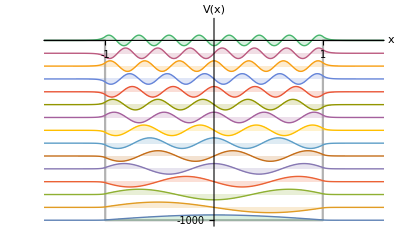

```mathematica
V0=1000;
Nn = 1998;
dq = 4.0/(Nn+1);
q0=-2;
OneHuge=VNWellsMod[V0,1,Nn,q0];
Mat1 = FDSchrodingerMat[OneHuge,Nn,dq,q0];big1=PlotVectorsListMod[OneHuge,Mat1,Nn,dq,q0,15,V0,1.5]
```

### Fifty Wells

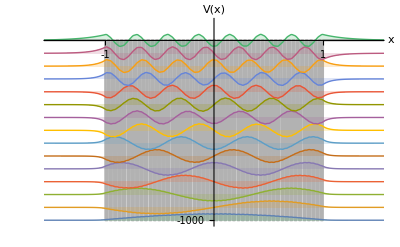

```mathematica
V0=1000;
Nn = 1998;
dq = 4.0/(Nn+1);
q0=-2;
FiftyHuge=VNWellsMod[V0,50,Nn,q0];
Mat50 = FDSchrodingerMat[FiftyHuge,Nn,dq,q0];
big50=PlotVectorsListMod[FiftyHuge,Mat50,Nn,dq,q0,15,V0,1.25]
```

## Wavefunction Comparisons

### Check Normalization

We should make sure that we’re getting Σ|ψ|^2=1 for both 50 and 1 wells.

#### 1 Well

First we need to find the lowest energies, and pull out the corresponding wavefunctions. Let’s compare the first 3 wavefunctions.

```mathematica
{energy1,wave1}=Eigensystem[Mat1];
locations1=Flatten[Table[Position[energy1,Sort[energy1][[i]]],{i,1,30}]]
```

{1951,1952,1953,1955,1956,1957,1959,1960,1962,1964,1966,1968,1970,1973,1975,1978,1981,1983,1987,1991,1998,1997,1996,1995,1994,1993,1992,1990,1989,1988}

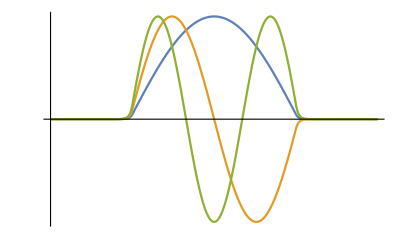

```mathematica
ListLinePlot[wave1[[locations1[[1]];;locations1[[3]]]],Ticks-> None]
```

#### 50 Wells

```mathematica
{energy50,wave50}=Eigensystem[Mat50];
locations50=Flatten[Table[Position[energy50,Sort[energy50][[i]]],{i,1,30}]]
```

{1965,1966,1967,1969,1970,1972,1974,1976,1978,1980,1983,1985,1988,1992,1996,1998,1997,1995,1994,1993,1991,1990,1989,1987,1986,1984,1982,1981,1979,1977}

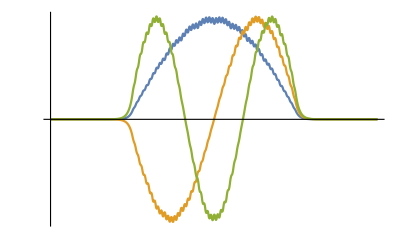

```mathematica
ListLinePlot[wave50[[locations50[[1]];;locations50[[3]]]],Ticks-> None]
```

#### Normalization Check

For the first 3 wavefunctions then check  Σ|ψ|^2=1

```mathematica
Normalization1={Total[wave1[[locations1[[1]]]]^2],Total[wave50[[locations50[[1]]]]^2]}
```

{1.,1.}

```mathematica
Normalization2={Total[wave1[[locations1[[2]]]]^2],Total[wave50[[locations50[[2]]]]^2]}
```

{1.,1.}

```mathematica
Normalization3={Total[wave1[[locations1[[3]]]]^2],Total[wave50[[locations50[[3]]]]^2]}
```

{1.,1.}

So everything in normalized, nice!

### Fifty vs. One Wavefunction Residual

Let’s see how they look plotted on the same grid. The “sign” input will fix the waves incase they are opposite.

```mathematica
comp[i_,j_,n_,sign_]:=Module[{h},
ListLinePlot[
If[sign=="same",
{wave50[[j]],wave1[[i]]},
{-wave50[[j]],wave1[[i]]}],
 AxesLabel->{"x","ψ(x)"},PlotStyle-> Thick,PlotLabel->Subscript[ψ, n], Ticks-> {{{(Nn+2)/4,"-1"},{3(Nn+2)/4,"1"}},{Max[wave1[[i]]],-Max[wave1[[i]]] }},PlotRange->All]];
```

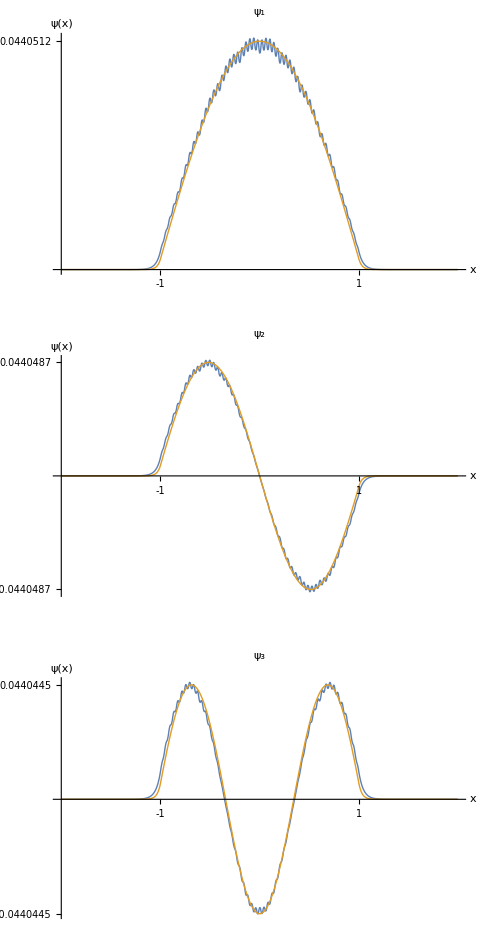

```mathematica
GraphicsGrid[{{comp[locations1[[1]],locations50[[1]],1,"same"]},{comp[locations1[[2]],locations50[[2]],2,"opposite"]},{comp[locations1[[3]],locations50[[3]],3,"same"]}}]
```

Now let’s find their difference.

```mathematica
res[n_,sign_]:=Module[{poten},
poten=VNWellsMod[Max[dif],50,1998,-2];Show[
ListLinePlot[
If[sign=="same",
dif=wave1[[locations1[[n]]]]-wave50[[locations50[[n]]]],
dif=wave1[[locations1[[n]]]]+wave50[[locations50[[n]]]]
], PlotStyle-> Thick,AxesLabel->{"x","Δψ"},PlotRange-> {{(Nn+2)/4-20,3(Nn+2)/4+20},Full},Ticks-> {{{(Nn+2)/4,"-1"},{3(Nn+2)/4,"1"}},{Max[dif],-Max[Abs[dif]],Max[dif]/2}},AxesOrigin->{(Nn+2)/4-20,0},PlotLabel->Style[Subscript[ψ, n],Large], AxesStyle->Larger],ListLinePlot[Table[poten[[i,2]],{i,1,1998}],PlotStyle->{Black,Opacity[0.4]}]]];
```

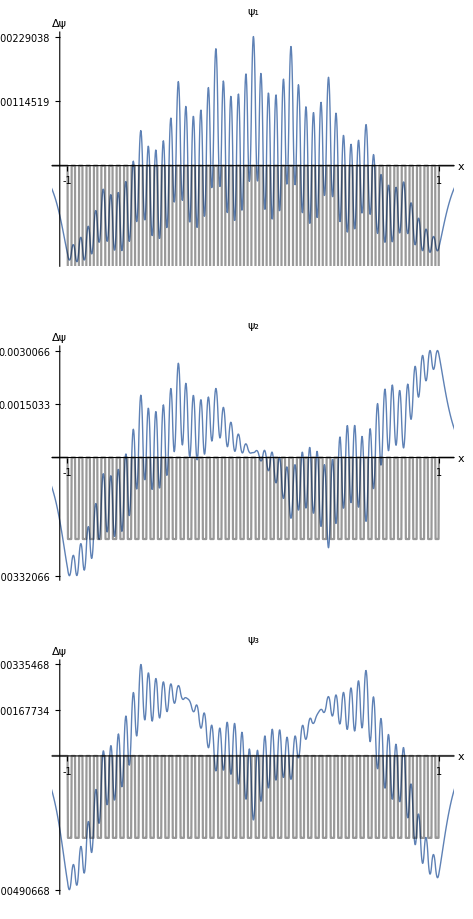

```mathematica
GraphicsGrid[{{res1=res[1,"same"]},{res2=res[2,"opposite"]},{res3=res[3,"same"]}}]
```

## Energies

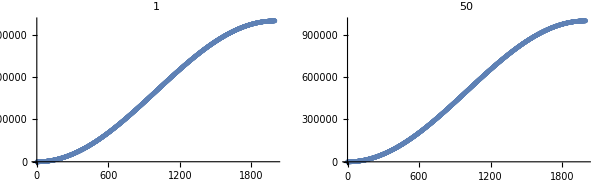

```mathematica
GraphicsGrid[{{ListPlot[Sort[energy1],PlotLabel->1],ListPlot[Sort[energy50],PlotLabel->50]}}]
```

```mathematica
{Max[energy1],Max[energy50]}
```

{998991.,998991.}

```mathematica
{Min[energy1],Min[energy50]}
```

{-997.679,-501.585}

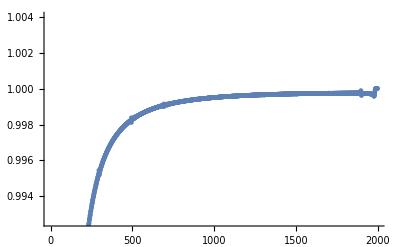

```mathematica
ListPlot[Sort[energy1]/Sort[energy50]]
```

#### Zooming In

What do the energies in both systems look like? Let’s plot them (orange is 50 wells, blue is 1 well):

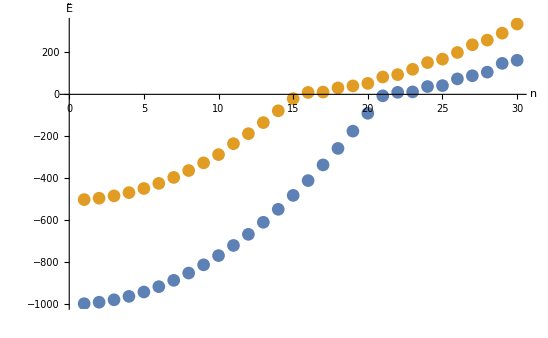

```mathematica
ListPlot[{Table[energy1[[locations1[[i]]]],{i,1,30}],Table[energy50[[locations50[[i]]]],{i,1,30}]}, AxesLabel->{"n","Ẽ"}]
```

```mathematica
energyratio=Table[energy1[[locations1[[i]]]],{i,1,30}]/Table[energy50[[locations50[[i]]]],{i,1,30}]
```

{1.98905,2.00163,2.02334,2.0554,2.09975,2.15937,2.23879,2.34501,2.48852,2.6763,3.06337,3.55896,4.52892,6.99431,23.4449,-45.1579,-31.2771,-8.38955,-4.35797,-1.73097,-0.0851824,0.1026,0.0969499,0.245515,0.248134,0.369225,0.375527,0.409407,0.50625,0.485022}

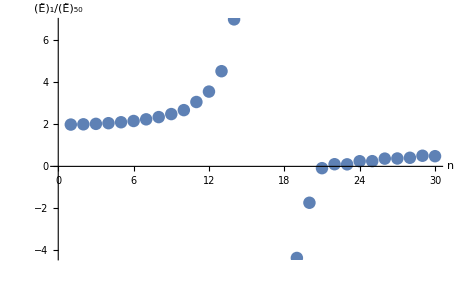

```mathematica
ListPlot[energyratio, AxesLabel->{"n","(Ẽ)_1/(Ẽ)_50"}]
```

```mathematica
FindFit[energyratio[[1;;15]],1.98 Exp[b1 n^4],{b1},n]
```

FindFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

{b1→0.998025}

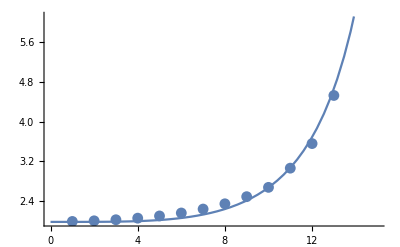

```mathematica
Show[Plot[1.98Exp[0.00003 n^4],{n,0,15}],ListPlot[energyratio]]
```

```mathematica
50/99.
```

0.505051

```mathematica
99./50
```

1.98

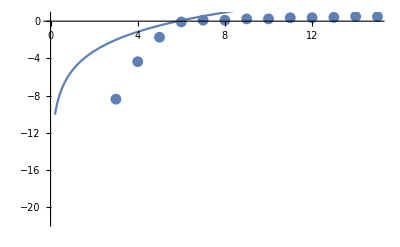

```mathematica
Show[ListPlot[energyratio[[16;;30]]],Plot[Log[.005 n^3],{n,-1,15}]]
```

## Energy Scaling of Wavefunctions

Similar to our initial function, this one nondimensionalizes the y axis and scales the energies accordingly.

```mathematica
PlotVectorsListModE[V_,Mat_,Nn_,dq_,q0_,Num_,V0_,s_]:=Module[{valpos,vector,vect,vec,vals,valsort,vecs,energies},
{vals,vecs} = Eigensystem[Mat];
valsort=Sort[vals];
energies=valsort/V0;
valpos=Flatten[Table[Position[vals,valsort[[i]]],{i,1,Num}]];
vector[n_]:= vecs[[valpos[[n]]]];
vect[n_]:= Table[{j dq+q0, 1/s(vector[n][[j]])+energies[[n]]},{j,1,Length[vecs[[1]]]}];
vec=Table[vect[n],{n,1,Num}];
Show[
 ListLinePlot[Table[{V[[i,1]],V[[i,2]]/V0},{i,1,Length[V]}], AxesLabel->{"x","E/V_0"}, Ticks-> {{1,-1},{-V0/V0,-0.50,-0.75,-0.25}},PlotStyle->{Black,Opacity[0.5]},PlotRange-> {{-2,2},{-1.01,If[Max[energies[[1;;Num]]]>1/10,.05+Max[energies[[1;;Num]]],1/10]}}, LabelStyle->Larger, AspectRatio->1 ],
ListLinePlot[vec, PlotStyle-> Thick,Ticks-> None,Filling->Table[(n)->(energies[[n]]),{n,1,Num}]]]]
```

#### 1

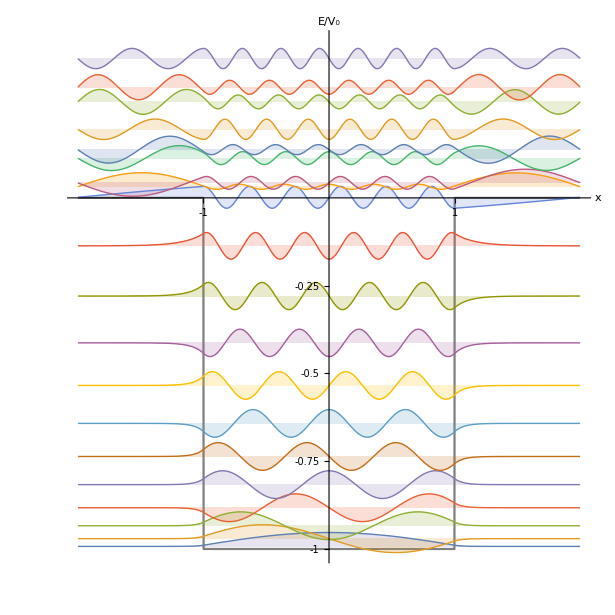

```mathematica
V0s=300;
Nns = 1998;
dqs = 4.0/(Nns+1);
q0s=-2;
OneHugescaled=VNWellsMod[V0s,1,Nns,q0s];
Matscaled1 = FDSchrodingerMat[OneHugescaled,Nns,dqs,q0s];
bigscaled1=PlotVectorsListModE[OneHugescaled,Matscaled1,Nns,dqs,q0s,20,V0s,1.1]
```

#### 50

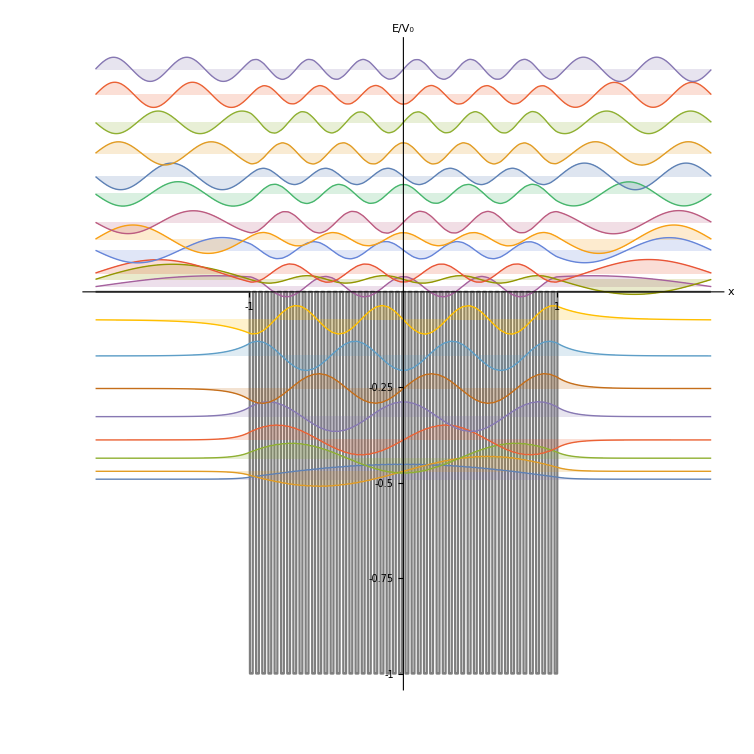

```mathematica
V0s=300;
Nns = 1998;
dqs = 4.0/(Nns+1);
q0s=-2;
FiftyHugescaled=VNWellsMod[V0s,50,Nns,q0s];
Matscaled50 = FDSchrodingerMat[FiftyHugescaled,Nns,dqs,q0s];
bigscaled50=PlotVectorsListModE[FiftyHugescaled,Matscaled50,Nns,dqs,q0s,20,V0s,1.1]
```

What is going on here!? Why are the waves starting from halfway up? Perhaps it’s because the “volume” of the 50 well case is about half that of the single well case?